```mathematica
bbpDelta[n_Integer,kmax_:4]:=Floor[Total[16^(1-#)/(8 #+Mod[n,7]+1)&/@Range[kmax]]]+1

twinPrimesBBP[limit_Integer,kmax_:4]:=Module[{pairs={},n=3},Reap[While[n<limit,If[PrimeQ[n]&&PrimeQ[n+2],Sow[{n,n+2}]];
n+=bbpDelta[n,kmax];]][[2,1]]]

twin=twinPrimesBBP[10^6];
GradientFieldPlot3D[...,PlotRange->All]
```

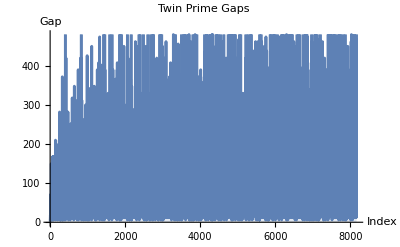

```mathematica
ListPlot[Differences[#[[All,1]]]&@twin,PlotLabel->"Twin Prime Gaps",Joined->True,Filling->Axis,AxesLabel->{"Index","Gap"}]
```

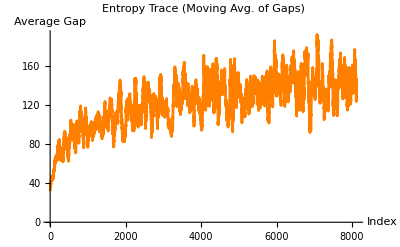

```mathematica
ListLinePlot[MovingAverage[Differences[#[[All,1]]]&@twin,50],PlotLabel->"Entropy Trace (Moving Avg. of Gaps)",AxesLabel->{"Index","Average Gap"},PlotStyle->Orange]
```

```mathematica
FourierListPlot[Differences[#[[All,1]]]&@twin,PlotLabel->"Fourier Spectrum of Twin Prime Gaps",AxesLabel->{"Frequency","Magnitude"}]
```

FourierListPlot[{2,6,6,12,12,18,12,30,6,30,12,30,12,6,30,12,30,12,30,36,72,12,30,60,48,30,18,24,18,150,12,6,30,24,138,12,18,12,30,60,78,48,12,12,18,108,24,30,6,120,12,48,30,24,66,84,6,54,18,48,30,54,6,24,18,12,96,30,42,30,42,168,42,66,30,24,18,60,12,168,30,120,48,84,6,42,30,30,12,18,72,6,60,12,18,24,90,96,54,30,66,12,72,18,30,42,36,30,60,12,12,18,12,66,84,60,36,30,90,12,72,66,12,132,36,42,12,78,132,48,138,24,36,24,18,120,12,6,84,108,18,12,210,42,66,72,30,60,90,102,18,90,30,12,60,18,12,36,42,78,12,168,84,96,24,18,108,30,60,12,30,168,120,72,60,78,132,12,60,96,42,108,60,30,192,18,24,108,30,12,30,198,42,60,78,12,6,24,168,48,42,48,90,72,78,30,30,24,48,132,30,30,96,30,42,30,180,150,30,48,120,12,48,42,12,180,138,60,150,18,60,54,108,30,72,30,36,54,78,12,126,162,72,210,96,84,6,210,120,60,282,12,18,12,36,72,48,24,30,66,12,72,168,72,66,60,102,12,30,36,240,270,132,18,42,30,222,60,6,84,6,150,84,90,6,72,48,42,132,90,180,18,42,138,72,78,48,162,18,84,96,30,72,90,18,60,24,66,42,48,72,12,36,30,54,6,12,60,12,120,36,24,210,18,372,6,162,60,42,30,168,42,6,42,72,156,54,90,48,72,30,30,126,84,126,84,36,30,42,90,78,30,24,36,90,84,30,6,42,132,126,60,114,30,36,30,12,12,36,90,102,198,54,18,48,114,6,90,114,60,30,48,18,60,42,120,102,66,12,18,144,90,78,168,24,66,42,18,54,90,78,198,72,192,48,498,60,54,138,132,6,102,60,108,24,198,48,84,66,114,138,12,420,18,12,18,132,18,12,60,108,48,132,42,126,72,48,12,42,108,48,12,42,126,24,156,12,72,96,30,42,60,138,24,48,42,90,270,108,78,180,12,168,102,90,120,132,78,48,132,120,78,24,66,282,12,18,210,42,30,30,66,72,72,120,30,180,6,42,78,180,30,60,24,48,108,24,48,42,30,90,30,48,108,84,30,78,30,30,102,78,30,108,42,18,240,12,18,132,18,42,18,204,96,30,54,48,42,66,102,30,12,78,60,108,84,6,114,90,30,198,168,60,24,60,138,72,36,60,114,96,234,126,60,252,12,108,30,90,180,108,30,24,186,24,18,102,90,30,180,246,90,120,12,108,42,42,18,42,36,174,120,120,66,12,102,30,138,318,12,198,90,24,276,102,108,60,150,294,36,24,30,156,24,108,90,150,90,108,24,36,54,108,42,60,126,54,108,72,60,138,60,150,270,78,144,36,30,42,132,6,102,72,66,60,42,72,66,12,102,150,90,78,72,348,18,42,138,24,246,234,228,42,90,90,36,42,90,150,90,90,48,12,228,90,204,36,30,240,42,12,30,36,30,312,192,96,72,60,108,30,54,48,42,36,12,120,42,90,48,30,78,54,36,24,18,120,18,120,72,48,132,18,54,30,30,78,132,198,90,42,300,78,90,72,66,42,102,6,72,18,42,240,48,60,42,102,96,114,108,72,180,168,150,42,186,60,24,60,36,12,270,42,18,108,180,114,390,18,78,42,42,48,288,132,168,114,6,102,180,12,30,156,84,30,108,60,108,30,30,210,24,30,66,114,96,84,18,12,270,30,48,60,18,180,30,234,108,210,42,18,60,138,24,48,12,150,186,120,102,12,30,156,12,138,60,24,30,156,42,420,12,66,90,390,12,102,126,12,18,234,180,48,90,90,420,150,12,48,108,630,42,12,6,42,168,114,78,30,168,12,48,42,150,312,36,114,150,126,84,120,96,42,108,72,72,96,180,72,18,42,120,18,12,108,90,54,126,252,210,180,102,96,192,48,24,6,54,138,18,150,180,174,180,96,72,168,42,222,108,60,18,132,120,42,66,144,90,6,240,24,66,30,72,72,120,18,42,18,180,78,30,84,48,222,36,42,30,30,18,264,66,12,48,24,60,78,162,96,72,210,12,66,54,6,24,18,198,180,24,198,168,24,300,246,72,168,252,60,42,180,30,96,102,108,12,30,252,156,42,180,12,138,78,90,282,12,78,78,102,108,54,120,108,180,42,90,276,24,6,150,60,12,60,138,24,426,54,246,72,30,30,210,108,90,174,78,168,162,72,60,6,114,30,60,96,150,60,24,216,24,18,138,42,12,66,30,54,78,108,24,6,150,84,90,180,96,54,198,30,42,36,30,102,78,132,120,60,30,162,6,30,54,78,330,12,36,72,60,162,78,78,342,120,42,96,30,42,132,108,180,48,12,108,114,108,132,30,66,24,168,48,150,12,102,96,84,180,60,18,162,96,300,84,108,30,30,42,30,258,30,18,30,42,12,78,240,42,258,78,132,120,18,54,138,12,6,252,450,42,36,60,12,150,78,120,54,126,174,30,36,90,90,60,144,258,18,30,12,12,216,90,114,240,156,210,42,162,18,60,108,72,30,12,108,72,96,174,108,12,30,198,12,66,144,60,48,78,24,96,102,42,156,42,48,42,90,12,18,90,198,102,138,102,42,210,348,12,156,30,192,42,108,258,150,60,24,180,156,12,132,66,12,120,48,30,30,42,138,54,6,12,150,288,24,66,174,78,72,18,78,60,30,12,18,204,6,120,90,180,180,12,270,162,210,30,126,30,252,312,6,42,48,72,222,30,216,90,162,60,18,24,96,54,48,108,90,180,84,150,18,138,24,198,102,30,390,30,126,12,12,96,60,84,78,72,90,78,132,78,42,48,378,24,108,168,240,264,90,66,30,60,42,132,90,78,42,90,30,78,102,108,30,408,210,120,174,96,84,96,90,84,36,210,84,90,66,12,180,30,30,252,18,48,102,42,168,12,6,474,156,24,66,162,90,60,42,108,90,108,42,222,240,48,48,42,198,180,42,48,24,210,30,156,162,102,18,42,66,12,12,156,30,24,156,84,96,42,18,264,156,402,42,18,30,108,222,132,150,18,42,108,132,168,12,78,18,24,30,48,120,90,342,6,150,102,138,114,150,48,90,42,126,42,78,54,30,108,30,42,96,12,180,42,36,162,210,180,102,186,12,30,162,6,120,132,108,30,12,72,78,72,60,66,30,612,48,180,24,78,42,108,180,18,72,138,30,24,156,162,78,12,12,96,54,6,114,66,12,102,96,12,42,90,126,510,114,60,30,150,390,60,66,54,36,12,78,114,228,12,126,72,138,102,288,132,150,108,30,84,216,264,120,246,174,48,138,30,42,318,72,30,108,294,90,36,102,72,108,30,108,90,84,108,30,12,138,102,66,114,96,30,60,42,12,276,282,60,108,42,210,12,18,192,168,102,138,198,30,162,72,66,60,54,48,108,282,108,90,180,42,12,96,90,330,42,30,192,90,78,102,168,108,204,48,30,30,192,90,156,84,96,192,72,66,42,42,30,6,132,48,72,192,66,90,330,84,120,48,42,18,42,60,48,90,42,96,30,222,528,42,168,102,60,132,30,48,120,228,324,78,102,66,90,132,72,306,102,348,132,78,54,48,30,78,30,24,288,42,276,12,168,30,60,84,108,138,60,432,18,90,60,30,84,108,132,150,240,66,84,180,48,192,90,6,240,72,60,348,120,504,36,54,78,42,36,174,36,42,12,36,240,84,138,162,210,96,42,108,72,18,222,222,390,90,48,102,168,198,24,30,60,78,72,126,42,12,48,90,168,72,30,12,30,66,84,18,108,72,60,120,120,12,78,78,210,180,114,78,30,18,42,120,72,96,42,228,162,78,54,36,30,60,12,42,336,24,18,72,66,42,180,18,60,42,132,198,138,102,12,366,24,36,132,78,24,30,66,294,18,30,48,120,84,210,120,180,156,42,138,132,12,30,168,168,30,162,72,186,120,102,42,108,168,12,42,6,72,78,132,78,30,102,162,210,90,126,390,12,408,24,156,192,30,60,42,66,54,78,108,54,48,12,390,138,18,12,60,42,126,90,372,120,102,78,90,12,30,108,42,48,318,102,138,222,72,150,48,42,66,42,138,102,72,378,120,12,156,84,18,180,18,174,216,162,48,264,240,36,114,6,12,582,48,252,66,72,42,60,6,174,96,150,42,30,102,180,156,84,588,150,30,270,108,60,150,24,78,372,60,138,210,252,18,168,222,288,30,84,6,84,150,66,72,132,90,408,48,204,18,78,504,168,18,84,66,72,240,72,36,240,30,30,180,72,138,102,192,168,60,78,12,312,240,126,24,156,24,30,30,30,36,72,168,90,42,48,42,48,12,102,66,12,18,114,90,198,222,246,84,78,48,150,30,24,156,12,90,90,48,72,42,90,126,90,24,450,198,12,66,30,30,102,78,54,48,72,108,60,48,252,210,48,204,60,138,12,90,96,60,42,108,60,90,30,84,18,120,18,30,42,30,48,162,48,84,168,18,54,216,162,210,18,120,60,12,60,138,54,156,54,216,84,216,120,24,18,180,72,66,30,72,300,162,36,114,66,72,12,126,204,66,72,78,102,102,66,60,54,108,198,60,12,78,120,132,162,6,270,924,30,78,78,24,108,102,96,42,48,54,126,180,54,96,420,210,90,42,180,252,108,48,42,108,12,48,24,30,108,78,54,30,360,126,24,120,36,84,30,18,258,90,204,198,222,210,48,12,66,132,198,414,180,6,180,114,180,198,192,6,192,42,198,108,222,42,120,108,102,120,168,138,42,30,12,186,30,114,180,66,12,252,36,90,90,24,366,12,60,42,96,114,336,12,102,138,12,60,120,450,486,60,60,132,90,192,48,42,6,270,54,6,234,66,162,348,114,126,54,276,102,12,18,12,30,36,12,30,198,114,36,102,60,192,138,30,30,78,72,90,150,42,66,174,180,186,24,240,288,42,90,96,72,30,132,228,180,90,42,246,42,90,12,138,30,12,150,48,78,174,30,138,138,114,66,42,12,78,108,192,42,30,30,210,66,90,210,12,42,96,102,108,264,126,42,42,198,210,102,138,12,90,66,12,270,72,90,30,186,12,42,276,462,198,264,156,72,252,336,60,24,180,270,36,42,228,354,210,108,228,294,336,54,180,18,78,132,120,18,84,198,108,30,24,6,42,108,42,18,330,72,102,336,42,90,78,90,252,18,30,294,96,240,30,84,36,144,36,42,450,42,348,18,24,30,138,102,30,198,12,126,84,36,60,234,36,54,66,42,12,36,150,444,48,138,30,42,12,156,24,96,102,108,132,78,72,12,78,150,60,780,168,84,60,66,54,6,24,156,54,30,138,18,12,162,258,180,72,96,270,84,210,78,42,240,60,36,42,18,24,546,102,120,90,12,96,114,66,84,30,48,288,300,42,48,114,18,78,90,24,18,330,30,48,174,210,90,78,60,18,90,162,78,84,30,18,132,210,18,210,30,108,222,48,252,42,210,108,72,18,168,90,132,138,192,42,18,252,126,24,120,66,12,48,222,150,18,30,234,66,132,222,126,24,78,318,270,222,72,96,12,12,90,90,18,72,528,168,114,66,42,78,204,168,198,150,42,312,156,42,282,138,192,6,210,90,240,294,168,18,192,102,30,120,48,42,180,138,60,78,114,276,72,210,390,282,30,156,84,30,6,450,60,84,78,258,30,174,18,270,42,246,54,48,42,30,36,54,168,48,12,72,138,12,186,192,102,30,66,102,120,138,270,54,138,72,6,42,42,78,42,180,6,120,60,24,90,348,228,24,240,288,18,60,42,318,114,78,450,240,12,198,18,90,120,24,18,12,30,168,180,12,168,42,108,30,858,84,246,210,240,30,42,108,120,42,90,168,72,210,240,102,96,252,12,60,216,120,252,78,54,48,12,156,204,78,108,144,78,102,318,132,48,102,186,24,150,6,120,120,210,12,282,306,204,36,54,168,72,168,162,210,18,180,18,204,6,132,258,54,150,48,108,264,210,330,78,60,42,198,162,30,108,90,42,486,132,90,30,90,150,60,48,42,42,78,108,30,360,72,192,36,132,132,156,24,66,174,30,78,90,162,156,24,30,210,60,96,30,12,192,6,150,60,234,96,72,90,12,30,48,42,90,36,30,42,18,162,60,558,12,228,24,30,6,24,156,42,138,42,168,42,600,42,60,108,30,192,90,210,36,330,150,222,72,66,132,198,42,180,12,66,84,30,156,180,42,48,174,18,60,210,12,30,330,258,42,180,78,252,258,120,300,30,162,126,12,30,90,12,330,18,102,6,324,216,84,108,42,96,180,162,168,120,30,24,36,150,102,258,60,282,12,60,48,78,54,66,72,30,210,360,72,156,390,240,72,138,42,108,72,420,60,180,120,30,42,30,66,120,84,168,12,138,72,78,18,270,90,144,96,90,84,306,84,36,30,132,90,198,72,30,72,36,240,84,66,72,12,6,84,66,222,162,6,270,54,18,12,66,132,138,84,306,90,84,48,162,306,180,42,222,168,180,330,180,168,120,84,120,78,60,30,12,78,18,12,30,72,600,180,18,402,30,60,90,36,12,168,204,60,66,204,66,210,42,210,180,12,90,288,240,438,30,84,600,138,168,12,132,6,330,300,42,48,42,120,240,432,6,24,48,300,228,30,54,18,150,42,60,78,60,12,486,342,180,168,12,42,198,270,12,66,42,18,210,330,60,54,6,90,114,18,450,42,108,18,174,6,84,66,72,102,108,252,60,90,30,126,90,174,90,150,6,174,18,108,282,252,138,42,78,288,114,60,66,30,42,378,84,150,90,66,102,288,54,78,42,90,240,60,66,240,24,18,408,24,138,18,72,168,114,126,120,84,60,78,18,72,78,60,234,60,180,420,18,180,18,12,120,210,78,84,96,162,42,168,42,18,240,72,78,90,108,102,132,366,102,462,246,30,114,30,36,120,162,42,126,12,42,30,30,240,30,36,60,24,138,90,12,186,24,180,306,102,192,48,12,168,102,96,42,198,180,234,168,228,42,78,174,180,150,210,228,30,162,36,120,42,228,180,54,30,138,102,138,12,30,150,36,12,210,30,78,12,48,210,120,72,60,72,36,210,312,150,90,48,90,12,180,30,42,60,96,30,24,96,174,48,48,282,372,18,138,102,48,90,114,126,90,72,60,78,102,222,18,42,138,12,138,78,252,90,30,12,60,30,36,72,18,204,408,90,138,12,138,30,192,60,108,42,60,108,30,12,78,234,150,60,30,108,210,42,6,204,186,24,48,48,210,72,60,210,108,90,12,72,66,24,156,60,30,24,18,192,66,204,48,132,78,30,18,150,60,72,162,126,60,30,174,156,174,216,114,96,60,24,18,102,210,78,72,30,36,480,30,180,30,114,150,66,90,12,150,42,18,252,96,420,42,72,168,180,42,228,72,540,90,6,84,36,204,138,102,180,210,426,222,72,120,30,276,240,60,72,318,60,90,120,54,66,252,12,30,258,108,54,18,72,168,558,534,78,90,222,66,210,114,126,210,144,6,120,264,138,312,180,96,12,12,168,42,60,30,78,18,402,438,72,12,138,30,30,180,30,30,342,36,42,42,390,138,138,60,210,234,138,132,156,252,120,132,6,42,120,90,18,294,96,12,60,12,156,264,168,42,186,24,6,252,180,12,30,456,72,90,300,18,12,420,102,156,342,132,168,252,78,18,180,30,54,18,372,18,180,180,162,96,42,12,60,258,78,90,42,198,54,270,156,240,174,210,6,114,90,90,150,180,90,36,30,72,252,138,18,54,150,216,30,174,30,90,180,120,258,108,180,90,42,42,66,222,42,48,78,42,378,120,12,138,144,96,192,18,24,6,300,90,120,60,84,528,78,120,222,270,42,30,96,30,24,90,120,6,132,60,240,138,84,30,150,240,138,312,210,66,42,90,120,90,12,30,36,450,60,180,162,252,210,168,330,42,120,60,36,60,72,108,90,192,138,174,96,24,240,150,168,102,108,30,48,252,90,582,420,138,12,276,330,252,132,36,132,462,18,222,210,156,42,72,36,72,90,48,540,12,120,210,42,300,96,234,30,210,30,18,132,126,372,180,252,150,198,42,156,150,30,84,18,132,6,24,90,78,60,198,192,102,96,372,60,102,126,132,42,240,156,42,192,588,90,330,252,186,180,210,42,60,72,108,42,276,132,72,66,42,18,132,162,216,30,12,288,54,66,84,156,102,108,54,198,12,228,198,234,66,144,210,18,120,198,102,90,48,24,156,420,30,12,180,600,48,12,150,102,180,18,72,78,300,78,12,30,138,72,12,30,18,180,378,210,480,234,60,138,72,300,210,6,204,30,30,66,144,126,102,132,30,6,432,108,84,18,180,30,72,180,66,222,30,30,198,30,150,54,240,60,138,210,12,150,6,12,18,462,48,42,78,54,96,222,102,138,42,276,72,438,42,168,54,96,84,6,150,144,78,132,108,420,180,12,156,102,78,252,252,270,30,120,126,90,24,6,42,132,30,6,360,222,132,138,72,48,90,330,90,42,108,12,90,198,162,60,120,36,180,432,42,588,228,90,42,102,186,132,42,6,84,108,12,18,168,54,180,6,180,54,60,180,306,132,150,150,30,180,60,18,54,66,42,102,318,132,66,24,18,150,102,96,60,30,150,24,126,42,78,42,180,330,60,18,54,66,480,42,138,144,288,180,240,222,258,12,210,348,30,60,342,18,180,228,24,30,60,48,60,72,78,132,126,252,12,240,276,84,96,30,84,210,6,150,24,378,48,264,168,18,24,30,540,30,156,150,90,204,18,102,210,36,30,60,342,78,84,108,228,192,150,198,240,12,18,24,60,120,228,168,360,114,18,72,138,12,150,78,48,330,12,252,30,180,240,6,132,372,36,192,12,126,72,192,78,48,102,60,90,210,30,42,6,222,42,348,138,90,12,30,348,12,12,198,240,210,108,12,18,360,30,174,96,192,30,210,12,90,180,276,180,42,48,24,48,168,90,132,138,24,30,48,318,150,102,72,390,156,30,24,156,54,96,12,162,6,60,72,42,198,168,90,72,18,24,48,108,102,48,174,96,240,330,144,66,120,42,78,72,18,54,120,36,12,30,42,36,84,186,234,90,96,42,12,156,72,288,180,210,72,72,30,36,270,24,228,168,30,72,138,162,90,210,210,192,18,180,150,102,276,72,102,156,204,186,72,42,180,36,132,78,84,126,90,360,174,48,18,102,78,12,372,276,84,180,396,84,390,306,180,420,750,264,66,42,18,12,72,30,126,132,48,54,66,84,168,438,30,12,168,24,366,90,12,72,6,252,132,78,18,102,132,270,126,72,108,12,60,60,180,108,54,6,54,60,66,264,228,12,600,138,198,222,72,126,12,492,18,348,192,120,132,90,36,312,18,474,240,126,132,42,30,60,156,150,420,114,156,42,180,120,42,156,12,30,42,300,96,24,138,228,12,222,36,222,360,12,6,150,510,180,192,30,42,66,90,234,30,150,18,222,90,36,132,12,126,42,30,48,294,78,132,18,108,84,426,42,408,54,36,120,42,90,102,96,54,126,120,210,372,210,210,132,36,222,168,72,60,78,174,126,54,126,432,630,132,108,30,30,42,246,114,30,246,114,618,72,78,72,258,132,216,72,132,6,54,318,60,30,210,12,30,108,30,72,156,210,24,30,138,12,60,66,84,6,42,108,480,132,252,468,432,156,234,6,150,42,198,12,18,210,132,252,246,150,480,174,336,204,6,120,90,114,60,126,54,306,132,48,144,18,90,228,54,48,210,318,84,60,150,18,150,198,30,264,150,30,60,36,54,210,186,24,438,108,72,12,126,102,282,180,60,36,12,48,192,18,42,12,60,126,150,12,48,390,204,168,162,6,342,192,216,42,12,246,102,72,30,180,30,90,156,12,72,216,162,240,450,72,66,30,12,108,174,108,12,540,300,396,54,96,252,132,168,108,180,30,144,36,312,198,402,18,324,150,156,30,120,600,522,102,210,138,42,108,48,12,120,132,36,90,180,102,162,216,42,132,48,180,60,120,198,24,30,48,90,18,222,48,552,168,144,126,12,102,78,42,30,18,42,30,216,294,30,6,84,108,180,18,24,48,42,216,30,12,162,36,54,60,408,192,366,12,42,48,42,348,12,96,60,120,312,102,126,330,114,60,78,42,198,282,108,210,198,12,18,24,6,132,48,30,402,60,600,108,114,168,228,264,96,234,156,144,66,54,90,78,90,78,270,12,18,24,180,120,180,30,420,66,54,6,234,336,102,12,108,102,210,360,126,252,180,240,132,138,150,312,150,168,60,12,156,42,108,222,228,144,96,180,54,138,42,18,108,120,42,48,42,102,180,18,462,156,132,72,60,96,42,348,60,12,198,12,138,282,138,102,252,306,42,282,246,540,222,138,30,324,48,102,30,30,6,90,234,168,42,18,42,420,330,48,240,330,12,120,108,108,72,102,66,144,168,30,258,72,210,30,168,282,108,12,90,348,144,138,282,120,390,90,108,72,108,48,30,330,30,102,162,216,12,30,12,36,90,420,42,30,78,30,150,42,42,270,18,42,6,174,108,30,108,144,150,30,366,102,288,54,18,30,138,60,24,336,54,18,138,180,42,138,120,12,120,90,180,168,54,90,150,138,18,84,66,54,78,390,138,54,30,66,30,534,18,132,36,24,96,12,72,90,120,138,18,12,12,18,192,168,18,54,60,378,78,102,18,90,132,210,72,78,30,60,90,240,90,48,492,282,60,360,108,120,78,114,60,90,78,78,54,90,150,96,60,114,120,168,270,282,66,114,30,360,468,42,210,510,120,78,72,18,162,168,60,42,138,72,450,258,78,582,18,12,180,510,138,84,36,252,78,120,42,48,42,90,162,6,84,30,156,54,6,24,66,132,402,648,72,36,42,48,54,30,66,114,138,60,12,78,312,156,42,12,126,54,6,132,72,126,60,222,60,90,78,42,120,30,18,54,66,12,90,582,168,18,30,414,30,60,36,144,276,384,96,144,126,24,240,108,132,66,30,120,90,180,444,36,120,84,126,54,408,198,42,228,84,48,90,378,654,90,36,102,162,156,642,42,18,312,180,78,72,6,90,252,42,36,54,96,12,228,30,54,66,84,228,30,138,54,150,30,18,78,294,420,78,180,120,60,150,162,90,90,126,42,42,306,42,138,312,168,162,42,126,120,210,222,150,48,54,150,210,168,102,306,240,204,336,84,126,42,198,312,150,210,12,18,42,60,390,36,210,42,252,36,222,162,6,150,144,36,84,450,90,66,60,180,12,12,138,252,48,120,42,450,468,252,78,168,60,12,42,60,318,30,78,240,54,6,30,54,558,168,42,30,72,36,294,216,192,150,120,12,36,90,252,120,18,12,312,198,12,96,12,168,294,168,270,78,132,222,66,204,36,252,642,78,90,18,54,96,162,132,18,42,270,6,30,30,282,30,42,36,12,18,312,12,108,240,30,168,204,198,72,180,126,144,96,102,78,54,6,222,60,168,54,180,138,30,60,168,24,138,132,126,24,126,312,180,168,162,120,120,60,150,12,330,36,72,192,156,174,96,54,180,126,60,84,180,18,48,132,108,300,42,318,12,90,288,90,42,138,240,84,126,90,42,30,42,30,240,66,84,48,222,78,252,60,66,132,180,30,72,66,24,90,198,48,102,30,252,30,126,84,96,192,180,30,42,90,120,48,150,168,282,240,420,78,114,318,252,30,198,570,42,30,6,204,240,96,42,42,60,30,180,108,60,72,216,282,72,126,24,198,18,180,72,120,210,78,300,162,78,54,48,162,78,78,144,108,270,138,54,336,60,204,168,72,126,30,282,150,468,90,60,24,60,210,420,60,66,24,60,30,78,48,180,534,120,30,90,66,54,48,180,72,6,102,30,78,102,18,24,198,72,96,30,132,240,12,120,36,174,378,192,66,204,138,138,114,150,6,90,132,150,138,300,162,78,204,90,126,330,222,240,132,96,72,78,42,42,48,252,180,66,12,78,150,354,48,492,60,126,42,168,210,24,300,90,30,258,132,270,60,48,18,30,702,48,30,132,162,48,168,174,120,66,42,390,48,222,12,276,144,228,42,90,36,24,150,6,30,84,246,54,210,60,96,42,168,60,12,60,90,72,18,288,90,372,240,18,162,132,78,228,324,198,42,66,30,42,150,42,438,252,36,114,90,66,210,54,240,198,198,90,132,210,30,138,360,210,114,270,48,48,84,108,132,120,240,60,90,186,72,78,312,30,222,18,378,54,156,54,78,60,42,108,132,246,42,270,198,42,78,90,150,270,150,180,90,462,72,168,180,78,330,204,138,120,210,378,12,72,168,180,108,30,54,6,84,66,84,66,72,18,420,204,18,72,318,12,36,150,12,168,264,18,138,72,60,108,402,60,198,222,72,36,312,180,408,12,12,6,84,360,18,180,108,102,138,42,138,252,168,462,78,24,18,138,72,330,42,186,24,18,78,210,30,60,180,354,66,312,252,96,24,186,12,60,150,72,66,42,42,90,90,6,210,24,6,24,150,126,312,438,84,6,102,222,6,360,492,30,78,102,42,36,210,102,42,60,36,342,162,90,78,12,36,300,132,180,42,156,84,198,120,18,84,108,72,108,18,54,48,108,222,18,540,450,90,234,108,78,24,150,156,144,78,18,12,270,138,462,282,108,30,30,168,42,30,192,66,72,48,162,168,210,60,72,432,348,42,156,204,78,12,240,108,108,72,60,138,42,102,420,66,30,54,66,90,420,24,90,36,114,150,408,12,120,150,96,42,342,96,54,60,108,198,84,36,240,12,258,192,198,102,42,48,30,132,138,30,78,450,150,282,102,156,162,12,30,216,210,84,36,42,30,240,162,78,132,90,66,132,192,66,114,96,294,36,24,60,90,168,48,234,6,54,306,12,72,168,222,240,318,90,198,474,276,84,366,42,222,180,6,84,78,270,348,42,30,198,42,162,120,90,210,438,60,90,240,72,126,150,30,180,42,18,42,72,78,42,48,192,6,90,294,396,72,192,210,186,234,126,42,12,48,162,78,42,126,132,30,12,6,12,60,162,138,18,144,150,108,240,42,6,24,156,204,60,66,324,300,120,60,108,342,6,90,30,90,102,72,198,108,114,120,60,126,12,138,120,42,342,330,48,30,258,222,198,90,102,180,18,180,180,12,48,390,54,186,432,618,162,30,72,126,60,150,264,138,90,222,18,90,72,126,30,30,180,30,390,102,540,18,42,72,300,30,90,288,12,288,90,48,30,210,120,72,450,120,132,120,78,12,138,12,60,30,120,420,240,66,72,168,72,42,180,96,132,108,84,156,234,156,174,78,132,6,102,42,66,60,312,108,60,42,162,6,150,42,72,318,138,174,138,408,780,174,48,120,12,30,48,210,168,60,210,210,24,456,90,30,60,84,498,18,12,48,54,126,402,60,162,78,48,90,54,180,90,90,930,1008,138,270,24,66,312,222,18,210,120,30,18,222,42,30,408,132,6,114,78,228,150,90,12,138,390,240,234,126,42,90,30,42,96,252,180,12,210,30,138,132,48,42,126,90,240,42,318,192,198,30,252,360,90,42,36,102,270,120,18,114,90,90,36,30,294,198,12,156,870,240,12,252,288,48,72,78,84,30,180,438,168,42,138,42,18,90,72,30,18,42,468,144,30,36,84,156,144,120,270,18,90,330,150,318,252,168,102,18,12,198,84,150,150,6,324,288,48,174,48,108,474,120,168,108,402,132,108,282,30,66,90,24,60,138,120,120,258,132,150,12,120,78,102,156,42,42,48,312,168,102,120,180,156,60,12,60,78,30,114,366,210,42,420,132,18,108,144,30,240,48,258,42,120,42,246,234,30,78,540,360,12,96,204,6,144,138,138,102,198,84,210,240,36,30,264,156,54,138,60,378,390,132,120,210,132,498,168,60,114,216,30,84,408,192,18,60,210,48,174,108,210,30,180,60,240,42,486,390,492,72,66,90,12,138,84,60,36,210,60,264,396,204,60,120,90,120,36,12,162,36,90,414,120,126,30,150,90,222,210,30,150,30,42,60,36,90,24,228,378,252,78,60,114,318,30,108,30,60,42,300,60,42,186,12,372,36,420,174,18,192,408,60,252,180,30,198,12,156,132,282,336,270,234,60,126,42,192,96,72,18,492,42,6,480,114,36,102,180,30,312,306,24,30,156,30,84,6,102,570,90,150,12,60,60,96,24,60,126,210,180,210,84,180,336,282,102,90,6,114,90,30,228,108,54,120,48,132,330,60,180,186,42,108,114,126,24,186,180,294,48,12,30,456,60,234,138,30,18,372,120,108,72,72,66,264,138,18,252,528,60,282,168,12,42,180,168,132,180,66,30,24,30,186,210,492,48,330,12,30,48,60,42,72,126,54,66,300,180,12,252,216,132,378,84,48,180,12,30,150,408,420,42,138,312,570,90,156,234,18,120,12,606,24,36,90,30,60,12,30,390,12,60,198,330,228,30,12,12,180,138,90,168,150,72,72,390,168,690,132,336,132,42,348,102,66,72,162,18,192,18,12,228,210,252,126,12,228,162,270,390,222,336,72,12,180,90,138,42,66,30,54,378,132,36,414,78,18,240,462,132,300,198,90,252,36,90,120,54,78,72,96,72,18,210,420,252,120,312,96,174,126,384,36,180,12,198,12,108,300,24,6,174,258,12,210,408,162,120,36,12,72,300,36,42,18,54,66,132,138,192,198,90,84,36,132,120,102,36,450,84,30,228,150,12,48,132,90,246,114,6,54,126,42,318,42,48,24,96,90,84,36,12,72,60,666,132,432,240,138,198,120,60,60,42,342,450,156,222,30,12,186,24,216,120,72,30,30,12,240,150,186,174,456,24,210,30,66,90,234,66,144,528,132,36,84,156,180,60,30,84,30,120,168,18,150,30,12,138,42,198,282,18,294,138,30,42,66,102,168,42,120,12,18,60,12,390,30,96,42,60,132,678,240,42,276,24,120,138,372,120,36,72,42,186,180,264,96,90,252,318,264,210,306,132,30,360,102,96,84,288,18,192,30,90,42,318,168,150,342,252,66,174,48,48,30,42,138,120,72,180,72,90,48,300,198,300,30,270,54,138,30,30,72,90,270,186,84,138,42,78,78,24,150,396,12,102,30,6,30,114,198,198,24,348,90,48,84,36,84,258,198,42,18,12,12,606,24,426,414,30,126,84,60,120,138,120,252,126,42,258,102,18,84,108,12,258,78,342,150,138,102,138,180,54,468,180,228,384,6,162,120,258,294,240,90,330,90,66,12,222,168,510,252,108,12,198,210,618,84,18,222,138,72,78,288,42,12,78,162,78,312,150,60,156,42,180,168,54,180,168,42,186,12,150,42,456,612,282,366,54,150,96,42,60,60,330,210,762,6,60,84,30,138,198,24,30,270,36,474,210,48,150,312,30,426,102,150,18,60,132,102,126,42,390,12,168,210,72,168,240,108,132,180,30,210,12,66,72,18,84,126,120,90,84,78,252,30,48,12,78,18,252,228,192,108,252,18,324,138,72,150,6,54,168,42,108,12,36,84,90,30,30,60,90,30,126,114,108,132,138,102,6,60,42,12,126,222,42,168,270,30,78,204,66,60,84,90,270,60,216,132,78,114,18,180,30,12,168,108,30,342,90,408,390,60,24,120,276,294,108,90,222,516,84,6,84,36,462,18,12,72,36,102,192,330,90,210,36,24,108,78,42,48,204,168,42,36,210,264,48,420,78,300,234,6,414,18,108,312,72,168,48,90,12,138,42,180,132,156,54,156,342,30,378,42,90,48,114,18,192,6,300,300,252,108,54,48,30,78,102,42,240,138,180,42,360,120,138,42,246,60,180,42,60,582,18,102,48,30,60,378,204,270,156,24,48,132,30,18,12,66,30,72,660,30,90,78,210,90,102,102,258,60,228,84,90,18,150,720,168,222,102,6,72,282,18,42,348,120,48,360,450,60,180,24,210,390,198,60,72,126,174,126,252,102,30,330,210,30,48,1452,210,138,48,90,270,24,90,78,78,204,156,102,138,240,234,138,312,66,42,438,24,6,132,210,450,12,6,150,390,114,156,150,90,24,90,108,18,54,120,366,12,90,42,30,210,6,144,138,468,342,42,186,84,198,42,66,12,120,210,78,222,72,198,210,138,12,30,468,54,210,96,102,78,54,126,72,30,138,84,90,78,258,12,618,264,66,30,114,36,30,42,48,54,78,60,150,72,48,372,210,48,222,156,132,48,192,42,30,228,330,210,408,252,108,60,150,294,258,72,36,42,30,180,60,138,60,252,42,78,228,180,30,240,192,192,210,168,120,300,450,462,18,192,30,96,84,48,12,36,90,42,162,366,102,42,66,12,30,48,24,66,282,312,156,180,84,168,372,6,30,42,78,102,72,36,54,78,222,30,6,60,114,138,42,60,48,240,30,102,258,288,222,252,36,30,84,18,372,420,156,180,102,72,240,108,18,90,120,150,84,96,54,120,120,30,156,72,108,42,192,30,300,6,60,360,120,12,210,12,138,60,252,180,228,120,18,162,168,120,84,348,138,42,60,120,102,198,372,390,240,30,60,78,60,162,60,96,90,42,48,30,60,360,12,78,84,126,132,168,90,12,168,84,66,72,102,198,300,30,90,90,48,42,78,312,348,174,6,30,210,42,702,138,48,54,276,12,102,30,36,102,18,120,30,60,204,690,336,30,192,42,756,54,18,198,42,162,180,78,138,42,108,84,180,48,180,18,120,12,102,210,186,150,270,384,168,48,150,30,150,60,72,288,144,30,180,60,180,498,18,672,42,198,240,222,36,84,90,168,42,36,162,42,36,180,72,240,168,180,174,336,792,60,618,150,294,150,18,222,30,66,210,90,462,252,108,210,210,210,180,90,120,72,156,24,6,72,222,66,54,156,30,420,72,180,150,30,12,18,30,180,150,48,12,18,12,12,198,72,288,72,126,42,60,78,174,168,90,378,72,12,60,60,66,324,156,120,90,402,18,54,126,150,54,18,102,66,534,66,552,48,120,12,150,60,30,180,408,24,30,336,24,306,30,84,96,60,30,42,78,132,180,282,108,12,186,222,132,96,84,486,174,150,96,270,72,12,78,120,120,72,270,66,144,36,12,198,54,78,162,210,90,48,210,30,168,60,150,90,252,90,48,24,126,30,12,210,42,156,24,126,42,60,312,126,24,108,60,210,270,192,240,78,42,18,108,114,18,150,18,252,192,228,78,42,468,24,18,222,306,12,960,468,42,18,114,156,42,90,60,30,120,48,192,48,150,210,210,12,102,66,264,6,120,90,180,102,48,372,138,444,156,54,336,90,12,198,54,210,120,198,60,492,258,42,198,18,420,234,168,18,72,42,126,444,60,36,30,462,102,456,180,90,24,198,12,348,48,24,18,222,150,6,822,102,108,30,60,168,12,252,126,30,24,180,30,348,180,18,234,228,108,90,42,240,180,372,126,144,126,222,198,42,180,222,240,60,180,18,42,306,114,126,42,90,42,126,42,168,312,180,90,108,42,42,60,78,72,60,138,12,18,258,120,24,150,6,192,522,30,330,348,60,252,396,174,48,192,30,198,12,156,24,18,240,48,102,138,54,228,378,30,192,30,18,174,60,240,66,294,336,102,288,72,72,168,60,462,288,342,126,120,450,24,18,102,6,60,24,30,216,132,42,228,18,210,54,408,552,90,66,324,168,42,60,120,228,72,138,108,132,42,6,120,264,276,60,204,6,390,150,102,18,192,168,24,126,342,78,30,42,18,30,54,156,54,78,18,114,150,180,18,450,210,12,108,48,30,42,330,60,42,156,192,18,54,78,60,252,66,42,240,18,450,120,90,12,210,222,156,234,198,168,240,42,210,390,60,42,66,324,360,126,264,18,210,180,270,78,84,90,246,42,342,156,42,162,366,72,108,30,30,24,90,138,108,174,90,378,90,12,30,36,30,180,204,288,42,60,30,36,210,54,78,348,30,372,18,240,120,114,60,36,72,42,96,12,288,264,30,348,42,150,210,6,252,78,384,126,210,54,180,18,462,6,72,30,168,270,180,54,210,480,378,150,420,102,96,30,12,72,96,12,228,150,150,162,210,78,60,114,36,114,60,66,234,270,486,102,12,6,84,48,120,90,72,258,180,240,162,210,366,252,252,198,12,156,42,318,60,30,120,132,78,54,210,18,702,156,42,108,102,258,72,210,312,78,72,156,102,258,162,180,108,42,30,438,90,240,300,192,252,108,42,90,156,90,504,336,282,300,42,246,114,66,60,12,18,54,168,150,102,240,66,210,12,210,42,366,30,180,42,198,192,30,18,210,24,138,78,12,12,30,156,342,90,72,66,12,72,66,42,468,114,36,642,102,180,348},PlotLabel→Fourier Spectrum of Twin Prime Gaps,AxesLabel→{Frequency,Magnitude}]

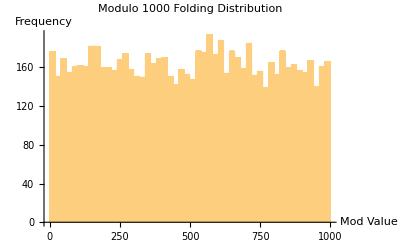

```mathematica
Histogram[Mod[#[[All,1]],1000]&@twin,50,PlotLabel->"Modulo 1000 Folding Distribution",AxesLabel->{"Mod Value","Frequency"}]
```

```mathematica
ListPointPlot3D[Table[{i,twin[[i,1]],twin[[i+1,1]]-twin[[i,1]]},{i,1,Length[twin]-1}],AxesLabel->{"Index","Prime","Gap"},PlotStyle->Directive[Blue,PointSize[Small]],Boxed->True]
```

-Graphics3D-

```mathematica
Show[%102,ViewPoint->Front]
```

-Graphics3D-

```mathematica
Show[%103,ImageSize->Large]
```

-Graphics3D-

```mathematica
Export["D:\\Nexus\\test.jpg",%104,"JPEG"]
```

D:\Nexus\test.jpg

```mathematica
Histogram3D[Table[{i,twin[[i+1,1]]-twin[[i,1]]},{i,Length[twin]-1}],{100,50},AxesLabel->{"Index","Gap"},PlotLabel->"Twin Prime Decoherence Volume"]
```

-Graphics3D-

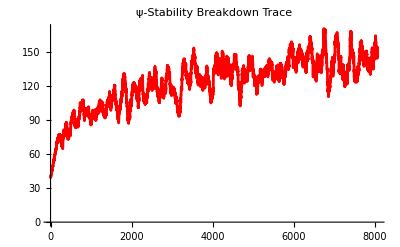

```mathematica
ListLinePlot[MovingAverage[Differences[#[[All,1]]]&@twin,100],PlotStyle->Red,PlotLabel->"ψ-Stability Breakdown Trace"]
```

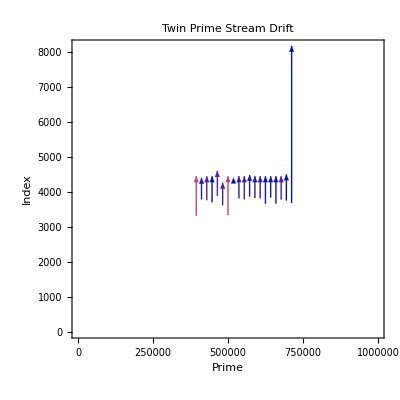

```mathematica
ListStreamPlot[Table[{{twin[[i,1]],i},{1,twin[[i+1,1]]-twin[[i,1]]}},{i,1,Length[twin]-1}],StreamPoints->Fine,StreamStyle->Blue,PlotLabel->"Twin Prime Stream Drift",AxesLabel->{"Prime","Index"}]
```